# Notebook 05: Transforming Graphics

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Example: Radio Tower

Suppose we want to draw something like a radio tower. We can start by drawing a few lines to get the basic shape, and put a little ball on top.

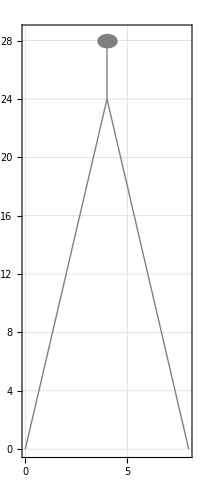

```mathematica
Graphics[{Gray,Thick,Line[{{0,0},{4,24},{8,0}}],Line[{{4,24},{4,28}}],Disk[{4,28},1/2]},Frame->True,GridLines->Automatic]
```

We can add some radio waves by drawing concentric circles of thin, dot-dashed lines. (When we are done with the dashing we turn it off with Dashing[None]). These circles will all have the same centre point and differing radii.

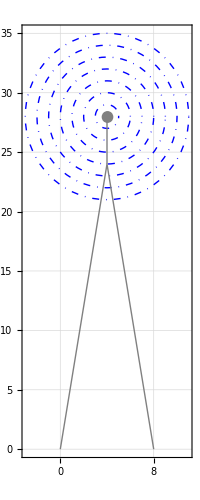

```mathematica
Graphics[{Blue,DotDashed,Table[Circle[{4,28},r],{r,1,7}],Gray,Thick,Dashing[None],Line[{{0,0},{4,24},{8,0}}],Line[{{4,24},{4,28}}],Disk[{4,28},1/2]},Frame->True,GridLines->Automatic]
```

We can turn our commands into a drawing function with relative coordinates.

```mathematica
drawRadioTower[{x_,y_}]:=
{Blue,DotDashed,Table[Circle[{x+4,y+28},r],{r,1,7}],Gray,Thick,Dashing[None],Line[{{x,y},{x+4,y+24},{x+8,y}}],Line[{{x+4,y+24},{x+4,y+28}}],Disk[{x+4,y+28},1/2]}
```

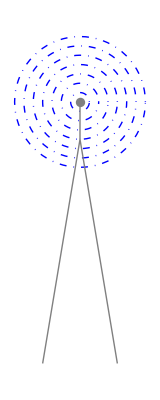

```mathematica
Graphics[drawRadioTower[{0,0}]]
```

Now suppose we want to add some support structures inside the body of the tower. We could do some criss-crossed lines like show below.

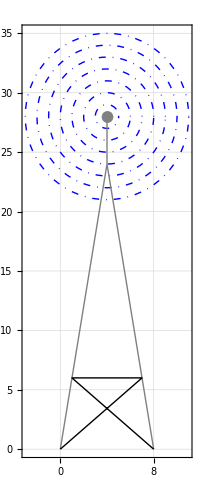

```mathematica
Graphics[Join[{drawRadioTower[{0,0}],Line[{{0,0},{7,6},{1,6},{8,0}}]}],Frame->True,GridLines->Automatic]
```

Let’s turn that into a function, too.

```mathematica
drawSupport[{x_,y_}]:=
{Gray,Line[{{x,y},{x+7,y+6},{x+1,y+6},{x+8,y+0}}]}
```

If we try to repeat our support structure, however, we see that it needs to get narrower each time we draw it. We will find that it is much easier to create pictures if we can transform graphic elements: move them around, change their scale, rotate them, etc.

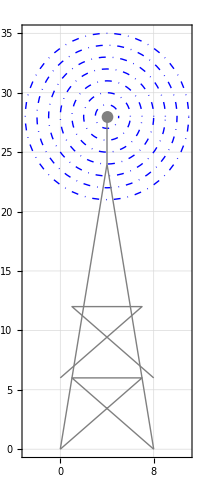

```mathematica
Graphics[Join[{drawRadioTower[{0,0}],drawSupport[{0,0}],drawSupport[{0,6}]}],Frame->True,GridLines->Automatic]
```

## The Scale command

The Scale command allows us to change the size of an object, either uniformly, or by different factors along different axes.

```mathematica
drawUFO[{x_,y_}]:=
{Orange,Disk[{x,y},{3,1}],LightOrange,Disk[{x,y+1/2},{3/2,1}]}
```

In the image below, I’ve drawn our original UFO, one that is uniformly scaled to half the size and one that is uniformly scaled to twice the size.

```mathematica
Graphics[{drawUFO[{0,0}],Scale[drawUFO[{7,0}],1/2],Scale[drawUFO[{16,0}],2]},Frame->True,GridLines->Automatic]
```

-Graphics-

To make something narrower or wider while maintaining its height, we scale along the x axis but not the y axis.

```mathematica
Graphics[{drawUFO[{0,0}],Scale[drawUFO[{7,0}],{1/2,1}],Scale[drawUFO[{16,0}],{2,1}]},Frame->True,GridLines->Automatic]
```

-Graphics-

To make something taller or shorter while maintaining its width, we scale along the y axis but not the x axis.

```mathematica
Graphics[{drawUFO[{0,0}],Scale[drawUFO[{7,0}],{1,1/2}],Scale[drawUFO[{16,0}],{1,2}]},Frame->True,GridLines->Automatic]
```

-Graphics-

### Adding supports to the radio tower

By scaling the supports each time we use them, we can get the desired effect on our radio tower.

```mathematica
Graphics[Join[{drawRadioTower[{0,0}],drawSupport[{0,0}],Scale[drawSupport[{0,6}],{.7,.9}],Scale[drawSupport[{0,11}],{.46,.7}],Scale[drawSupport[{0,15}],{.26,.57}],Scale[drawSupport[{0,18}],{.16,.33}]}]]
```

-Graphics-

### Scaling a complex graphic element

If we bundle the full radio tower into a drawing function, we can now scale it as a whole, too.

```mathematica
drawFullRadioTower[{x_,y_}]:=
Join[{drawRadioTower[{x,y}],drawSupport[{x,y}],Scale[drawSupport[{x,y+6}],{.7,.9}],Scale[drawSupport[{x,y+11}],{.46,.7}],Scale[drawSupport[{x,y+15}],{.26,.57}],Scale[drawSupport[{x,y+18}],{.16,.33}]}]
```

```mathematica
Graphics[{LightGray,Rectangle[{0,0},{50,15}],drawFullRadioTower[{0,0}],Scale[drawFullRadioTower[{11.5,0}],3/4],Scale[drawFullRadioTower[{22,0}],1/2],Scale[drawFullRadioTower[{33,0}],1/4],Scale[drawFullRadioTower[{38.5,0}],1/8]}]
```

-Graphics-

### Relative proportions

The Scale command can be very useful for getting the relative proportions of an image right.

Here are the pieces we need to draw a stop sign, but it doesn’t look very good.

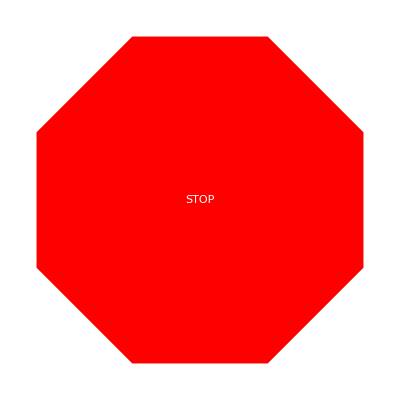

```mathematica
Graphics[{Red,Polygon[CirclePoints[8]],White,Text["STOP"]}]
```

This version uses three scaled polygons on top of one another to get the white boundary. Note that we use the FontSize attribute of the Style command to increase the size of the text.

```mathematica
Graphics[{Red,Polygon[CirclePoints[8]],White,Scale[Polygon[CirclePoints[8]],.95],Red,Scale[Polygon[CirclePoints[8]],.9],White,Text[Style["STOP",Bold,FontSize->100]]}]
```

-Graphics-

## The Translate command

The Translate command allows us to move an element along the x axis, y axis or both.

Here is a blue disk, along with a green disk that has been translated 2 units along the x axis (i.e., to the right), and a red disk that has been translated -3 units along the same axis (i.e., to the left). Note that the coordinates given to all three disks are {0, 0}. Their relative movement is caused by the Translate command.

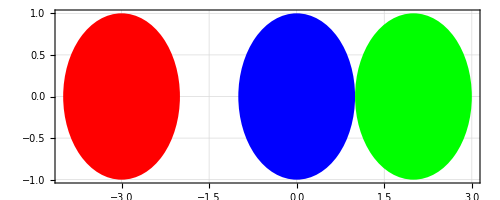

```mathematica
Graphics[{Blue, Disk[{0,0},1], Green, Translate[Disk[{0,0},1],{2,0}],Red,Translate[Disk[{0,0},1],{-3,0}]},Frame->True,GridLines->Automatic]
```

The pair of coordinates given to the Translate command is often referred to as a ‘vector’, and visualized with an arrow. In the figure below, the translation vector is {3, 4}.

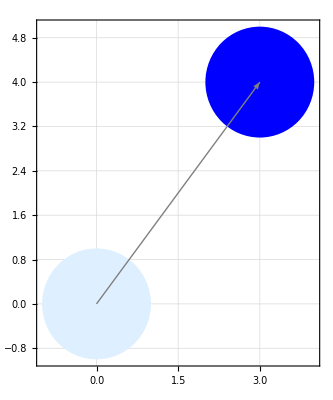

```mathematica
Graphics[{LightBlue, Disk[{0,0},1], Blue, Translate[Disk[{0,0},1],{3,4}],Gray,Thick,Arrow[{{0,0},{3,4}}]},Frame->True,GridLines->Automatic]
```

We don’t have to translate elements from the origin. Compare this figure with the previous one: note the difference in centre coordinates for the two disks, and note how we adjusted the position of the arrow.

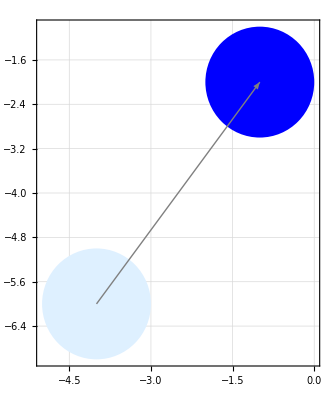

```mathematica
Graphics[{LightBlue, Disk[{-4,-6},1], Blue, Translate[Disk[{-4,-6},1],{3,4}],Gray,Thick,Arrow[{{-4,-6},{-4+3,-6+4}}]},Frame->True,GridLines->Automatic]
```

## The Rotate command

The Rotate command allows us to rotate an element by a specified angle. We can use either degrees or radians to specify the angle.

Here are 4 UFOs. The second, third and fourth are rotated 45, 90 and 135 degrees respectively.

```mathematica
Graphics[{drawUFO[{0,0}],Rotate[drawUFO[{10,0}],45Degree],Rotate[drawUFO[{20,0}],90Degree],Rotate[drawUFO[{30,0}],135 Degree]},Frame->True,GridLines->Automatic]
```

-Graphics-

Note that angles are measured from a horizontal line and increase in a counterclockwise manner. If we want to rotate in the clockwise direction, we specify negative angles.

```mathematica
Graphics[{drawUFO[{0,0}],Rotate[drawUFO[{10,0}],-45Degree],Rotate[drawUFO[{20,0}],-90Degree],Rotate[drawUFO[{30,0}],-135 Degree]},Frame->True,GridLines->Automatic]
```

-Graphics-

## Tables of Transformations

By using the Table command with various transformations, we can make many interesting designs.

```mathematica
Graphics[{Blue,Table[Rotate[Circle[{0,0},{3,1}],r Degree],{r,0,330,30}]}]
```

-Graphics-

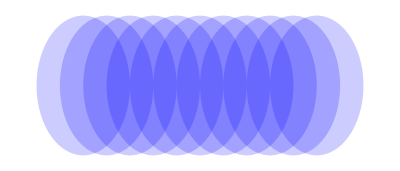

```mathematica
Graphics[{Blue,Opacity[.2],Table[Translate[Disk[{0,0},{2,3}],{x,0}],{x,0,10}]}]
```

```mathematica
Graphics[{Blue,Opacity[.2],Table[Scale[Rectangle[{0,0},{2,3}],s],{s,1,9}]}]
```

-Graphics-

Combining Scale and Rotate

```mathematica
Graphics[{Blue,Opacity[.2],Table[Rotate[Scale[Rectangle[{0,0},{2,3}],s],s*15Degree],{s,1,9}]}]
```

-Graphics-

```mathematica
Graphics[{Blue,Table[Rotate[Scale[Circle[{0,0},{2,3}],s],s*15Degree],{s,1,9}]}]
```

-Graphics-

## In-Class Activity

### Draw a picture using the Graphics command. Use Scale, Rotate and Translate in your picture.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course